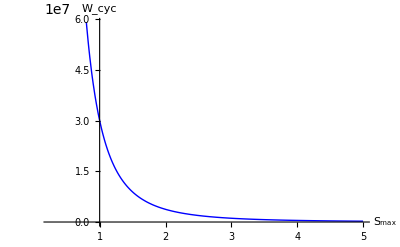

```mathematica
sigmay=500000000;
b=2;
k=0.2;
Wcyc=2*(b-1)*Smax^(b+1)/(k*(b+1)*(b+2)*sigmay^(b-1));
Wf=50000000000000000000000;
Nf=Wf/Wcyc;
Plot[Nf,{Smax,sigmay/20,sigmay},
TicksStyle->Directive[Black,20],AxesStyle->Thick,AxesLabel->{Style["S_max",Black,24],Style["W_cyc",Black,24]},PlotStyle->{Blue,Thick},AspectRatio->0.618]
```

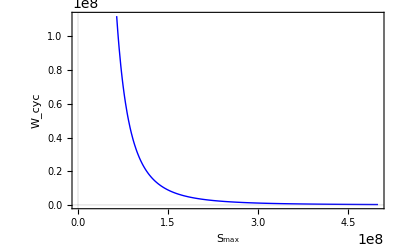

```mathematica
Plot[Nf,{Smax,0,sigmay},PlotTheme->"Scientific",TicksStyle->Directive[GrayLevel[0],20],AxesStyle->Thickness[Large],AxesLabel->{Style["\!\(\*SubscriptBox[\(S\), \(max\)]\)",GrayLevel[0],24],Style["\!\(\*SubscriptBox[\(W\), \(cyc\)]\)",GrayLevel[0],24]},PlotStyle->{RGBColor[0,0,1],Thickness[Large]},AspectRatio->0.618]
```

```mathematica
Show[%74,ImageSize->Full]
```

-Graphics-

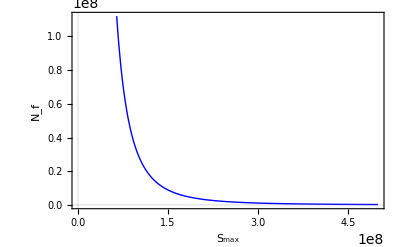

```mathematica
Show[%75,AxesLabel->{None,None},FrameLabel->{{HoldForm[Subscript[N, f]],None},{HoldForm[Subscript[S, max]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Arial",25,GrayLevel[0]}]
```